Plot a 2 D area element.

```mathematica
<<peeters` ;
<<MaTeX`

SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 18]
peeters`setGitDir[ "../project/figures/classicalmechanics" ]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→18,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

\\wsl$\Ubuntu\home\pjoot\project\figures\classicalmechanics

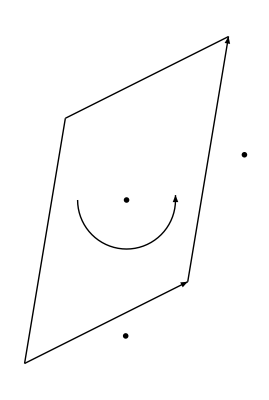

```mathematica
ClearAll[o,a,b, r, rm, ar, br, rad, center, e1, e2]
o ={0,0};
a = {1,0.5};
b = {0.25,1.5};
e = 0.2;
r = {{1,-1},{1,1}}/Sqrt[2];
rm = {{1,1},{-1,1}}/Sqrt[2];
rad = 0.3;
center = (a+b)/2;
e1 = {1,0};
e2 = {0,1};
ar = rm.a;
br = rm.b;

p = Graphics[{
Thick,
Arrowheads[.05],
Arrow[{o,a}],
Line[{o,b}],
Arrow[{a,a+b}],
Line[{a + b,b}],

Circle[center,rad,{-2Pi/2,0}],
Arrow[ {center+rad e1 ,center+rad e1 + 0.03 e2}],

Text[ MaTeX["d\\mathbf{x}_u = \\frac{\\partial x}{\\partial u} du"],  0.9 a/2 + 0.8 e ar],
Text[ MaTeX["d\\mathbf{x}_v = \\frac{\\partial x}{\\partial v} dv"], a + 0.8 b/2 +  e br],
Text[ MaTeX["d\\mathbf{x}_u \\wedge d\\mathbf{x}_v"], center]

}]
```

```mathematica
peeters`exportForLatex["areaElementParallelographFig1", p]
```

{areaElementParallelographFig1.eps,areaElementParallelographFig1pn.png}